#### 圆管扰流问题有限元求解

1. 指定计算区域

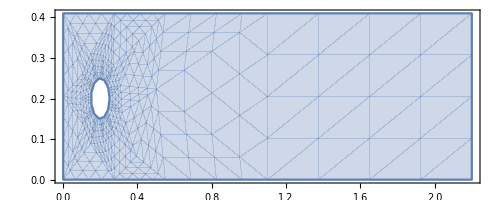

```mathematica
rules={length->22/10,hight->41/100};
Ω=RegionDifference[Rectangle[{0,0},{length,hight}],Disk[{1/5,1/5},1/20]]/.rules;
region=RegionPlot[Ω,AspectRatio->Automatic]
```

2. 二维不可压缩流动的N-S方程如下（需说明的是：CFD中将连续方程、动量方程（NS）和能量方程统称为N-S方程或Euler方程，这点与理论流体力学习惯不同）

```mathematica
op = {ρ*D[u[t,x,y],t]+({{-μ,0},{0,-μ}}.u[t,x,y]{x,y}Inactive){x,y}Inactive+ρ *{{u[t,x,y],v[t,x,y]}}.u[t,x,y]{x,y}Inactive+D[p[t,x,y],x], 
ρ*D[v[t,x,y],t]+({{-μ,0},{0,-μ}}.v[t,x,y]{x,y}Inactive){x,y}Inactive+ρ *{{u[t,x,y],v[t,x,y]}}.v[t,x,y]{x,y}Inactive+D[p[t,x,y],y], 
D[u[t,x,y],x]+D[v[t,x,y],y]}/.{μ->10^-3,ρ->1};(*N-S方程*)
```

3. 边界条件

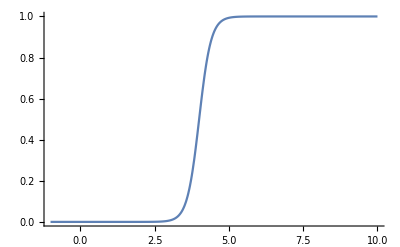

```mathematica
rampFunction[min_,max_,c_,r_]:=Function[t,(min*Exp[c*r]+max*Exp[r*t])/(Exp[c*r]+Exp[r*t])]
sf=rampFunction[0,1,4,5];
Plot[sf[t],{t,-1,10},PlotRange->All]
```

```mathematica
bcs={DirichletCondition[u[t,x,y]==sf[t]*4*1.5*y*(hight-y)/hight^2,x==0],DirichletCondition[u[t,x,y]==0.,0<x<length],
DirichletCondition[v[t,x,y]==0,0≤x<length],DirichletCondition[p[t,x,y]==0.,x==length]}/.rules;
```

4. 初值条件

```mathematica
ic={u[0,x,y]==0,v[0,x,y]==0,p[0,x,y]==0};
```

5. 有限元求解

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
Dynamic["time: "<>ToString[CForm[currentTime]]]
AbsoluteTiming[{xVel,yVel,pressure}=NDSolveValue[{op=={0,0,0},bcs,ic},{u,v,p},{x,y}∈Ω,{t,0,10},
Method->{
"TimeIntegration"->{"IDA","MaxDifferenceOrder"->2},
"PDEDiscretization"->{"MethodOfLines",
"DifferentiateBoundaryConditions"->True,
"SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.0005}}}},EvaluationMonitor:>(currentTime=t;)];]
```

{138.802,Null}

```mathematica
{minX,maxX}=MinMax[xVel["ValuesOnGrid"]](*最小最大速度范围*)
```

{-0.604146,2.16991}

6. 计算结果可视化

```mathematica
mesh=xVel["ElementMesh"];(*形成网格，以提高可视化效率*)
```

```mathematica
AbsoluteTiming[frames=Table[Rasterize[ContourPlot[xVel[t,x,y],{x,y}∈mesh,PlotRange->All,AspectRatio->Automatic,ColorFunction->"TemperatureMap",Contours->Range[minX,maxX,(maxX-minX)/12],Axes->False,Frame->None,ImageSize->800,PlotPoints->100],ImageResolution->100],{t,3,10,1/12}];]
```

{272.487,Null}

```mathematica
frames//ListAnimate
```

```mathematica
DensityPlot[xVel[10,x,y],{x,y}∈mesh,PlotRange->All,AspectRatio->Automatic,ColorFunction->(Hue[0.7-0.7#]&),PlotLegends->BarLegend[Automatic,LegendMarkerSize->200],Axes->False,Frame->None,ImageSize->800,PlotPoints->200]
```

-Graphics-

```mathematica
densityPlotList=Table[Rasterize[DensityPlot[xVel[t,x,y],{x,y}∈mesh,PlotRange->All,AspectRatio->Automatic,ColorFunction->(Hue[0.7-0.7#]&),Axes->False,Frame->None,ImageSize->800,PlotPoints->200,PlotLegends->BarLegend[{Hue[0.7-0.7#]&,{minX,maxX}},LegendMarkerSize->200]],ImageResolution->150],{t,0,10,0.2}];
```

```mathematica
ListAnimate[densityPlotList]
```

```mathematica
Export["F://圆柱绕流.GIF",densityPlotList[[36;;-1]],"DisplayDurations"->0.2,AnimationRepetitions->Infinity]//SystemOpen
```

说明：另一种交互办法(可局部交互，也可用于全局交互)

```mathematica
k=1;Animator[Dynamic[k],{1,Length[densityPlotList],1}]
```

```mathematica
Dynamic@densityPlotList[[k]]
```